# Orthogonal Columns Fat

I had a random double orthogonalization thought!

```mathematica
m=624;
Q=RandomReal[{-1,1},{m,m}];
Q=Orthogonalize[Q];
QQ=Orthogonalize[Q];
QQt=Orthogonalize[Qᵀ];
QQr=Orthogonalize[Reverse[Q]];
QQrt=Orthogonalize[Reverse[Q]ᵀ];
Map[Norm[#.#ᵀ-IdentityMatrix[m]]&, {Q,QQ,QQt,QQr}]
```

{2.82338×10^-15,2.35939×10^-15,3.11971×10^-15,2.82389×10^-15}

The question at hand is how is for a given Q how is 
	Q . u 
distributed for random unit vectors u.  This is the same as asking how the entries of the unit vector are distributed. The sum of the squares of the components is 1.   I believe (see below) that the square of the first entry of the vector is distributed as a beta distribution

```mathematica
?Histogram
```

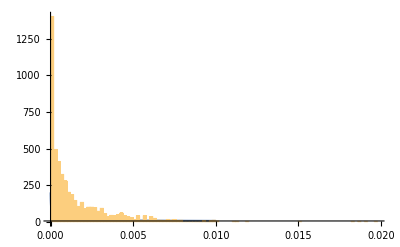

```mathematica
d=4;
f[x_]=PDF[BetaDistribution[1/2,(d-1)/2],x];
SampleSize=1234;
Data=Table[
u=RandomVariate[NormalDistribution[0,1],m];
u=Normalize[u];
u⟦1⟧^2,
{SampleSize}];
Show[
Plot[ f[x],{x, 10^-5,0.01},PlotRange->All],
Histogram[Data,100,"PDF"]]
```

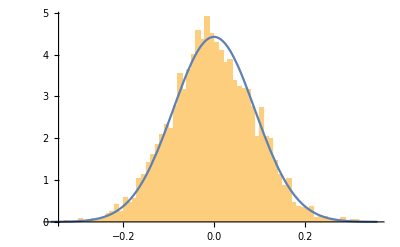

```mathematica
f[z_]=PDF[NormalDistribution[0,1/√m],z];
Show[
Histogram[Data,50,"PDF"],
Plot[f[x],{x,-4/√m,4/√m},PlotRange->All],
PlotRange->All]
```

## Single Vectors

https://mathoverflow.net/questions/315221/distribution-of-the-individual-coordinates-of-a-uniform-random-vector-on-a-high

## Random Vectors

To sample a rotationally invariant unit vector in ℝ^m we can sample x~(N(0,1))^m and normalize to get u=x/||x||.    The question is how are individual components of u distributed

```mathematica
m=12;
x=RandomVariate[NormalDistribution[0,1],m]
s=x.x
u=x/√s
Norm[u]
```

### s~χ^2[m]

The sum of squares s=∑_(i=1)^m x_i^2 has Chi Squared distribution s∼χ^2(m)  with m degrees of freedom.  Essentially just the definition.

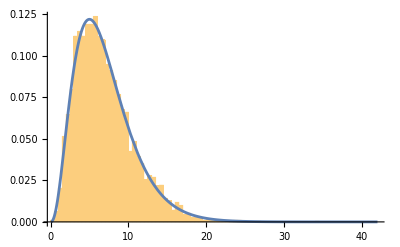

```mathematica
m=7;
SampleSize=4234;
Data=Table[
x=RandomVariate[NormalDistribution[0,1],m];
s=Norm[x]^2,{SampleSize}];
f[z_]=PDF[ChiSquareDistribution[m],z];
Show[
Histogram[Data,50,"PDF"],
Plot[f[x],{x,0.05, 6m},PlotRange->All],
PlotRange->All]
```

### u_1=N(0,1)/√s∼N(0,1/√m)

The individual entries of x=u/√s are the ratio of a standard normal divided by the square root of a χ^2 with m degrees of freedom.  If m is large then s is effectively independent of each individual u_i and can be well approximated by a  normal. I believe the correct scaling is 1/√m. I need to find a reference for this.

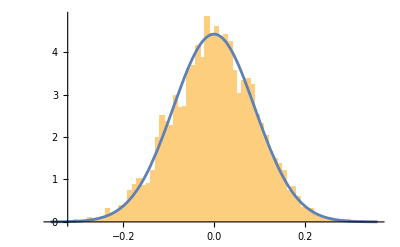

```mathematica
m=123;
SampleSize=4234;
Data=Table[
x=RandomVariate[NormalDistribution[0,1],m];
s=Norm[x]^2;
x⟦1⟧/(√s),{SampleSize}];
f[z_]=PDF[NormalDistribution[0,1/√m],z];
Show[
Histogram[Data,50,"PDF"],
Plot[f[x],{x,-4/√m,4/√m},PlotRange->All],
PlotRange->All]
```

## Random Matrices

### QᵀQ=I_r with Q∈ℝ^(m×r) and m>>r

I run the Gram-Schmidt process on (A~N(0,1))^(m×r) to generate Q.  If I am being careful, I need to pick the reflectors carefully if I do a Householder reflector. The result is a rotationally invariant sampler from the appropriate orthogonal space.   The question I have now is what do I need and how do I get it.

Maybe the answer is easier than I think. Maybe we can think slightly abstractly and use the rotational invariance over and over.

### I think P_1=Q Qᵀ is going to be a random projector and I-P_1 is the complement

```mathematica
m=123;
SampleSize=4234;
Data=Table[
x=RandomVariate[NormalDistribution[0,1],m];
s=Norm[x]^2;
x⟦1⟧/(√s),{SampleSize}];
f[z_]=PDF[NormalDistribution[0,1/√m],z];
Show[
Histogram[Data,50,"PDF"],
Plot[f[x],{x,-4/√m,4/√m},PlotRange->All],
PlotRange->All]
```

-Graphics-

## Break

```mathematica
RandomOrthAugment[Q_,s_Integer]:=Module[{m,n,S},
{m,n}=Dimensions[Q];
S=RandomReal[{-1,1},{m,s}];
S-=Q.Qᵀ.S;
QRDecomposition[S]⟦1⟧ᵀ]

RandomOrth[{m_,n_}]:=Module[{S},
S=RandomReal[{-1,1},{m,n}];
QRDecomposition[S]⟦1⟧ᵀ]
```

Testing

```mathematica
{m,n,s}={12,3,4};
Q=RandomOrth[{m,n}];
AugQ=RandomOrthAugment[Q,s];
BigQ=ArrayFlatten[{{Q,AugQ}}];
{Dimensions[Q]=={m,n},Dimensions[NewQ]=={m,s},
OrthogonalMatrixQ[Q],
OrthogonalMatrixQ[BigQ]}
```

{True,True,True,True}

## Making Low Rank Matrices

```mathematica
LowRankBuild[{m_,n_},σs_]:= Module[{U,V,r=Length[σs]},
{U,V}=Map[RandomOrth[{#,r}]&, {m,n}];
U.DiagonalMatrix[σs].Vᵀ]
```

Testing

```mathematica
{m,n}={123,56};
σs=Sort[{1,2,3,4,5,6,7,8,9.3}];
A=LowRankBuild[{m,n},σs];
{Dimensions[A]=={m,n}, Norm[σs-Sort[SingularValueList[A]]]}
```

{True,4.08224×10^-15}

## Basic Algorithm: Initialization

I need to initialize the algorithm with a “consistent” low rank approximation.

```mathematica
LowRankInit[A_,s_]:= Module[{m,n,SL,SR,TwoSidedSample,
σ, Tol=10^-15,U,S,V},
{m,n}= Dimensions[A];
{SL,SR}=Map[RandomOrth[{#,s}]&,{m,n}];
TwoSidedSample=SLᵀ.A.SR;
σ=SingularValueList[TwoSidedSample, Tolerance->Tol];
{U,S,V}=SingularValueDecomposition[TwoSidedSample,Length[σ]];
{SL.U,Diagonal[S],SR.V}
]
```

Testing.  If the

```mathematica
{m,n}={123,56};
σs=Sort[{1,2,3,4,5,6,7,8,9.3}];
A=LowRankBuild[{m,n},σs];
s=12;
{U,σ,V}=LowRankInit[A,s];
{OrthogonalMatrixQ[U],OrthogonalMatrixQ[V],Length[σ],
Norm[Uᵀ.A.V-DiagonalMatrix[σ]]}
```

{True,True,9,1.74387×10^-15}

## Low Rank Iterate

The no truncation iteration iteration is pretty easy.

```mathematica
LowRankUpDateNoTruncation[A_,{U_,σ_,V_}, {sL_,sR_}]:= Module[
{m,n,UA,VA,ReSample,UIn,σIn,VIn},
{m,n}=Dimensions[A];
{UA,VA}= MapThread[RandomOrthAugment,{{U,V},{sL,sR}}];
ReSample=ArrayFlatten[({{DiagonalMatrix[σ], Uᵀ.A.VA}, {UAᵀ.A.V, UAᵀ.A.VA}})];
{UIn,σIn,VIn}=SingularValueDecomposition[ReSample];
{ArrayFlatten[{{U,UA}}].UIn,Diagonal[σIn],ArrayFlatten[{{V,VA}}].VIn}
]
```

Testing.  The singular values

```mathematica
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1,2,3,4,5,6,7,8,1239.3}]];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,Length[σs]];
s=10;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
{UNew,σNew,VNew}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
rng={0,1.1σNew⟦1⟧};
ListPlot[{σ,σNew⟦1;;Length[σ]⟧}ᵀ,
PlotRange->{rng,rng},
Epilog->Line[{{0,0},{σNew⟦1⟧,σNew⟦1⟧}}]];
TableForm[{σ⟦1;;Length[σs]⟧,σNew⟦1;;Length[σs]⟧,σs,
σs/σNew⟦1;;Length[σs]⟧,σNew⟦1;;Length[σs]⟧/σ⟦1;;Length[σs]⟧}ᵀ,
TableHeadings->{Automatic,{"σ_0","σ_1","σ","σ_1/σ_0"}}]
```

| σ_0 | σ_1 | σ | σ_1/σ_0 | 
1 | 58.6302 | 78.1553 | 1239.3 | 15.8569 | 1.33302
2 | 0.349005 | 0.436102 | 8 | 18.3443 | 1.24956
3 | 0.200689 | 0.313503 | 7 | 22.3284 | 1.56213
4 | 0.152615 | 0.20359 | 6 | 29.471 | 1.334
5 | 0.0953648 | 0.146437 | 5 | 34.1445 | 1.53554
6 | 0.0508905 | 0.0787202 | 4 | 50.8129 | 1.54685
7 | 0.0255 | 0.0628873 | 3 | 47.7044 | 2.46617
8 | 0.00889661 | 0.0342188 | 2 | 58.4475 | 3.84627
9 | 0.00303192 | 0.0212313 | 1 | 47.1002 | 7.00259
10 | 6.81226×10^-9 | 1.0592×10^-7 | 0.00001 | 94.4105 | 15.5485

The rank is correct. The numerical rank is also correct: the relatively small singular value sample as relatively very small singular values. I am going to run this with a fixed truncation to the hard rank and see how the singular values converge. It looks as though the small ones make faster relative progress than the big ones. I think this is because the correct way to think about it is that the cluster is making progress.

#### Early Behavior

With one big singular value and one tiny singular value.  All things make progress.

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1,2,3,4,5,6,7,8,1239.3}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=200;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
{MaxIter}];

{Us,Vs}={Data⟦All,1⟧,Data⟦All,3⟧};
UDotU0=Table[
Table[Us⟦i,All,k⟧.U0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
VDotV0=Table[
Table[Vs⟦i,All,k⟧.V0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];

Residuals=Table[{U,σ,V}=Data⟦i⟧; Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],{i,MaxIter}]/Norm[A,"Frobenius"];

TabView[{
"σ_i/σ"->ListLogLogPlot[(Data⟦All,2⟧ᵀ)/σs,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic],
"u_i.u_0"->ListLogLogPlot[Abs[UDotU0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"v_i.v_0"->ListLogLogPlot[Abs[VDotV0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"||A-U_i.S_i.V_i(||)_F/||A(||)_F"->ListLogLogPlot[Residuals,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic]
}]
```

1234

With no big singular value and one tiny singular value.  All things make progress.

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1,2,3,4,5,6,7,8,9.3}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=200;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
{MaxIter}];

{Us,Vs}={Data⟦All,1⟧,Data⟦All,3⟧};
UDotU0=Table[
Table[Us⟦i,All,k⟧.U0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
VDotV0=Table[
Table[Vs⟦i,All,k⟧.V0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];

Residuals=Table[{U,σ,V}=Data⟦i⟧; Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],{i,MaxIter}]/Norm[A,"Frobenius"];

TabView[{
"σ_i/σ"->ListLogLogPlot[(Data⟦All,2⟧ᵀ)/σs,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic],
"u_i.u_0"->ListLogLogPlot[Abs[UDotU0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"v_i.v_0"->ListLogLogPlot[Abs[VDotV0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"||A-U_i.S_i.V_i(||)_F/||A(||)_F"->ListLogLogPlot[Residuals,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic]
}]
```

1234

Two identical small σs cause grief! for the small singular vectors. Not surprising.

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1.0 10^-5,1,2,3,4,5,6,7,8}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=200;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
{MaxIter}];

{Us,Vs}={Data⟦All,1⟧,Data⟦All,3⟧};
UDotU0=Table[
Table[Us⟦i,All,k⟧.U0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
VDotV0=Table[
Table[Vs⟦i,All,k⟧.V0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];

Residuals=Table[{U,σ,V}=Data⟦i⟧; Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],{i,MaxIter}]/Norm[A,"Frobenius"];

TabView[{
"σ_i/σ"->ListLogLogPlot[(Data⟦All,2⟧ᵀ)/σs,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic],
"u_i.u_0"->ListLogLogPlot[Abs[UDotU0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"v_i.v_0"->ListLogLogPlot[Abs[VDotV0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"||A-U_i.S_i.V_i(||)_F/||A(||)_F"->ListLogLogPlot[Residuals,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic]
}]
```

1234

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1.0 10^-6,1,2,3,4,5,6,7,1234,1233.8}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=200;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
{MaxIter}];

{Us,Vs}={Data⟦All,1⟧,Data⟦All,3⟧};
UDotU0=Table[
Table[Us⟦i,All,k⟧.U0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
VDotV0=Table[
Table[Vs⟦i,All,k⟧.V0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];

Residuals=Table[{U,σ,V}=Data⟦i⟧; Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],{i,MaxIter}]/Norm[A,"Frobenius"];

TabView[{
"σ_i/σ"->ListLogLogPlot[(Data⟦All,2⟧ᵀ)/σs,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic],
"u_i.u_0"->ListLogLogPlot[Abs[UDotU0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"v_i.v_0"->ListLogLogPlot[Abs[VDotV0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"||A-U_i.S_i.V_i(||)_F/||A(||)_F"->ListLogLogPlot[Residuals,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic]
}]
```

1234

Two close singular values cause some grief for the singular vectors.

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-6,1.0 10^-5,1,2,2.001,4,5,6,7,8}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=200;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
{MaxIter}];

{Us,Vs}={Data⟦All,1⟧,Data⟦All,3⟧};
UDotU0=Table[
Table[Us⟦i,All,k⟧.U0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
VDotV0=Table[
Table[Vs⟦i,All,k⟧.V0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];

Residuals=Table[{U,σ,V}=Data⟦i⟧; Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],{i,MaxIter}]/Norm[A,"Frobenius"];

TabView[{
"σ_i/σ"->ListLogLogPlot[(Data⟦All,2⟧ᵀ)/σs,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic],
"u_i.u_0"->ListLogLogPlot[Abs[UDotU0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"v_i.v_0"->ListLogLogPlot[Abs[VDotV0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"||A-U_i.S_i.V_i(||)_F/||A(||)_F"->ListLogLogPlot[Residuals,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic]
}]
```

1234

Two similar dominant singular values cause grief for the singular vectors!

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1,2,3,4,5,6,7,123,124}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=200;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
{MaxIter}];

{Us,Vs}={Data⟦All,1⟧,Data⟦All,3⟧};
UDotU0=Table[
Table[Us⟦i,All,k⟧.U0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
VDotV0=Table[
Table[Vs⟦i,All,k⟧.V0⟦All,k⟧,{i, MaxIter}],{k,1,Length[σs]}];
Residuals=Table[{U,σ,V}=Data⟦i⟧; Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],{i,MaxIter}]/Norm[A,"Frobenius"];

TabView[{
"σ_i/σ"->ListLogLogPlot[(Data⟦All,2⟧ᵀ)/σs,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic],
"u_i.u_0"->ListLogLogPlot[Abs[UDotU0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"v_i.v_0"->ListLogLogPlot[Abs[VDotV0],
PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
FrameLabel->{"iter","σ_i/σ_0"},
GridLines->Automatic],
"||A-U_i.S_i.V_i(||)_F/||A(||)_F"->ListLogLogPlot[Residuals,PlotRange->All,PlotLegends->σs,
Joined->True,Frame->True,
GridLines->Automatic]
}]
```

1234

I think there is useful information in the reconstruction long before the terminal convergence in Ben’s figures.

#### Late Behavior

As noted by Ben the later behavior is error = r^n

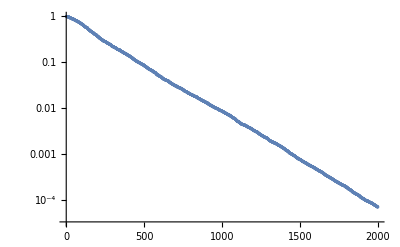

```mathematica
Clear[U,σ,V]
{m,n}={323,156};
σs=Reverse[Sort[{1.0 10^-5,1,2,3,4,5,6,7,8,1239.3}]];
r=Length[σs];
A=LowRankBuild[{m,n},σs];
{U0,σ0,V0}=SingularValueDecomposition[A,r];
s=r;
{U,σ,V}=LowRankInit[A,s];
{sL,sR}={3,3};
MaxIter=2000;
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧};
Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],
{MaxIter}]/Norm[A,"Frobenius"];
ListLogPlot[Data]
```

```mathematica
Data=Table[
{U,σ,V}=LowRankUpDateNoTruncation[A,{U,σ,V},{sL,sR}];
(* Hard Truncation *)
{U,σ,V}={U⟦All,1;;r⟧,σ⟦1;;r⟧,V⟦All,1;;r⟧},
Norm[A-U.DiagonalMatrix[σ].Vᵀ,"Frobenius"],
{MaxIter}]
```

$Aborted

```mathematica
σ
```

{1239.3,8.,7.,6.,5.,4.,3.,2.,1.,0.00001}